```mathematica
Array[f, 24]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11],f[12],f[13],f[14],f[15],f[16],f[17],f[18],f[19],f[20],f[21],f[22],f[23],f[24]}

```mathematica
f[1]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-350.0-500.0"];
f[2]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-500.0-645.0"];
f[3]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-657.0-691.0"];
f[4]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-710.0-715.0"];
f[5]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-740.0-759.0"];
f[6]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-767.0-810.0"];
f[7]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-844.0-890.0"];
f[8]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-350.0-500.0"];
f[9]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-500.0-645.0"];
f[10]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-657.0-691.0"];
f[11]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-710.0-715.0"];
f[12]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-740.0-759.0"];
f[13]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-767.0-810.0"];
f[14]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-844.0-890.0"];
f[15]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-350.0-500.0"];
f[16]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-500.0-645.0"];
f[17]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-657.0-691.0"];
f[18]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-710.0-715.0"];
f[19]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-740.0-759.0"];
f[20]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-767.0-810.0"];
f[21]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-844.0-890.0"];
```

```mathematica
f[22]=Import["/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-350.0-890.0"];
f[23]=Import["/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-350.0-890.0"];
f[24]=Import["/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-350.0-890.0"];
```

```mathematica
Array[n, 24]
```

{n[1],n[2],n[3],n[4],n[5],n[6],n[7],n[8],n[9],n[10],n[11],n[12],n[13],n[14],n[15],n[16],n[17],n[18],n[19],n[20],n[21],n[22],n[23],n[24]}

```mathematica
i=1; While[i<25, n[i]=NonlinearModelFit[f[i], a x^b, {a, b}, x, MaxIterations-> 100000]; i++]
```

```mathematica
Array[p, 24]
```

{p[1],p[2],p[3],p[4],p[5],p[6],p[7],p[8],p[9],p[10],p[11],p[12],p[13],p[14],p[15],p[16],p[17],p[18],p[19],p[20],p[21],p[22],p[23],p[24]}

```mathematica
j=1; While[j<25, p[j]=n[j]["ParameterConfidenceIntervalTable"]; j++]
```

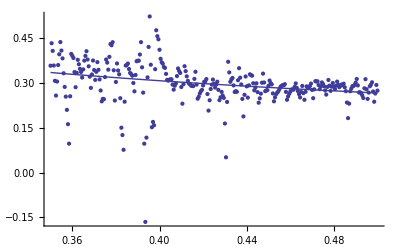

```mathematica
Show[ListPlot[f[1]], Plot[n[1][x], {x, 0.35, 0.5}]]
```

```mathematica
p[1]
```

| Estimate | Standard Error | Confidence Interval
a | 0.171041 | 0.0179544 | {0.135708,0.206374}
b | -0.641363 | 0.119192 | {-0.875925,-0.406801}

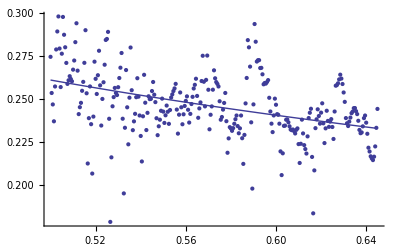

```mathematica
Show[ListPlot[f[2]], Plot[n[2][x], {x, 0.5, 0.645}]]
```

```mathematica
p[2]
```

| Estimate | Standard Error | Confidence Interval
a | 0.191431 | 0.0060225 | {0.179577,0.203284}
b | -0.447886 | 0.0551835 | {-0.556498,-0.339273}

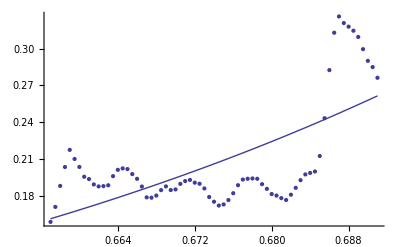

```mathematica
Show[ListPlot[f[3]], Plot[n[3][x], {x, 0.657, 0.691}]]
```

```mathematica
p[3]
```

| Estimate | Standard Error | Confidence Interval
a | 8.85892 | 4.67343 | {-0.469292,18.1871}
b | 9.53065 | 1.34986 | {6.83632,12.225}

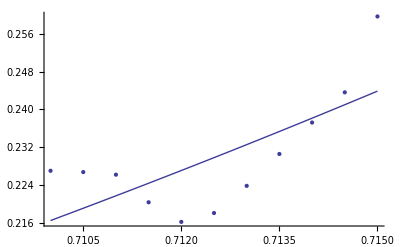

```mathematica
Show[ListPlot[f[4]], Plot[n[4][x], {x, 0.710, 0.715}]]
```

```mathematica
p[4]
```

| Estimate | Standard Error | Confidence Interval
a | 71.8678 | 137.05 | {-238.16,381.895}
b | 16.9492 | 5.62829 | {4.21707,29.6812}

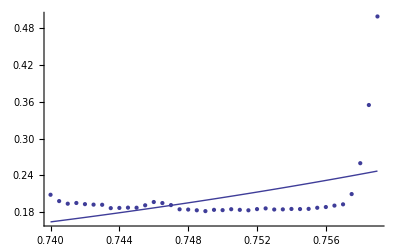

```mathematica
Show[ListPlot[f[5]], Plot[n[5][x], {x, 0.740, 0.759}]]
```

```mathematica
p[5]
```

| Estimate | Standard Error | Confidence Interval
a | 21.2367 | 34.0142 | {-47.6825,90.156}
b | 16.1522 | 5.58707 | {4.83171,27.4727}

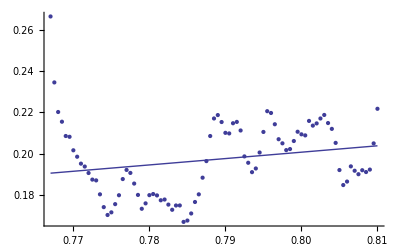

```mathematica
Show[ListPlot[f[6]], Plot[n[6][x], {x, 0.767, 0.810}]]
```

```mathematica
p[6]
```

| Estimate | Standard Error | Confidence Interval
a | 0.264228 | 0.0375644 | {0.18954,0.338916}
b | 1.2302 | 0.598194 | {0.0408293,2.41957}

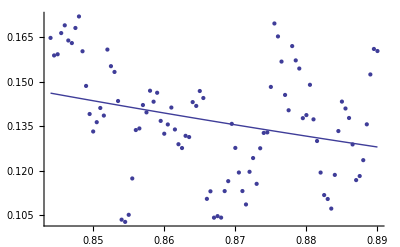

```mathematica
Show[ListPlot[f[7]], Plot[n[7][x], {x, 0.844, 0.890}]]
```

```mathematica
p[7]
```

| Estimate | Standard Error | Confidence Interval
a | 0.0955712 | 0.0120627 | {0.07161,0.119532}
b | -2.50469 | 0.871278 | {-4.23538,-0.774007}

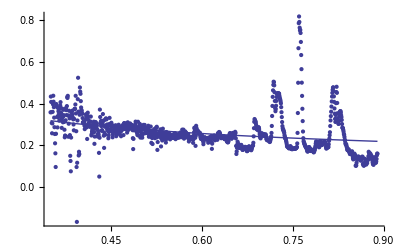

```mathematica
Show[ListPlot[f[22]], Plot[n[22][x], {x, 0.350, 0.890}]]
```

```mathematica
p[22]
```

| Estimate | Standard Error | Confidence Interval
a | 0.209696 | 0.00484676 | {0.200186,0.219206}
b | -0.397432 | 0.0367396 | {-0.469521,-0.325342}

```mathematica
Array[c,3]
c[1]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051.IRR"]
c[2]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312.IRR"]
c[3]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328.IRR"]
Array[nlm,3]
i=1;While[i<4,nlm[i]=NonlinearModelFit[c[i],a x^b,{a,b},x,MaxIterations->10000];i++]
Array[pwmo,3]
j=1;While[j<4,pwmo[j]=nlm[j]["ParameterConfidenceIntervalTable"];j++]
```

{c[1],c[2],c[3]}

{{0.368,0.32149},{0.412,0.33993},{0.5,0.274642},{0.61,0.223833},{0.675,0.173321},{0.778,0.185638},{0.862,0.128908}}

{{0.368,0.103941},{0.412,0.140975},{0.5,0.125028},{0.61,0.126214},{0.675,0.104322},{0.778,0.118859},{0.862,0.088936}}

{{0.368,0.307853},{0.412,0.352929},{0.5,0.291875},{0.61,0.249881},{0.675,0.211676},{0.778,0.214968},{0.862,0.187914}}

{nlm[1],nlm[2],nlm[3]}

{pwmo[1],pwmo[2],pwmo[3]}

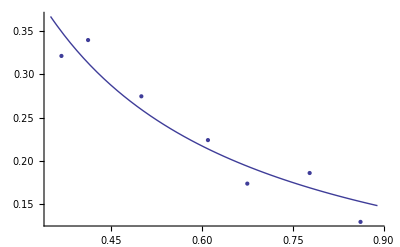

```mathematica
Show[ListPlot[c[1]], Plot[nlm[1][x], {x, 0.35, 0.89}]]
```

```mathematica
pwmo[1]
```

| Estimate | Standard Error | Confidence Interval
a | 0.131881 | 0.014049 | {0.095767,0.167995}
b | -0.975692 | 0.138208 | {-1.33097,-0.620417}